## Task 2 List Generation

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms"]
data=Import["task2_data.dat","List"];
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms

```mathematica
dataList=Table[StringTake[data[[i]],6],{i,1,Length[data]}];
```

{{110100,2877},{010101,2845},{011100,2808},{011101,276},{001100,79},{100100,69},{000101,86},{110001,7},{011000,73},{010100,60},{110101,297},{111100,283},{010001,87},{110000,86},{100110,1},{001010,10},{111000,8},{101100,6},{001101,3},{011001,6},{100101,7},{000100,2},{000011,10},{100010,6},{000111,1},{010000,1},{101010,1},{001011,2},{000001,1},{001000,1},{100000,1}}

```mathematica
Block[{t=SortBy[Tally[dataList],Last]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

Number | Frequency
000001 | 1
000111 | 1
001000 | 1
010000 | 1
100000 | 1
100110 | 1
101010 | 1
000100 | 2
001011 | 2
001101 | 3
011001 | 6
100010 | 6
101100 | 6
100101 | 7
110001 | 7
111000 | 8
000011 | 10
001010 | 10
010100 | 60
100100 | 69
011000 | 73
001100 | 79
000101 | 86
110000 | 86
010001 | 87
011101 | 276
111100 | 283
110101 | 297
011100 | 2808
010101 | 2845
110100 | 2877

## Task1-2 (The bit-string order is Reversed!)

```mathematica
graph={{0.3461717838632017,1.4984640297338632},{0.6316400411846113,2.5754677320579895},{1.3906262250927481,2.164978861396621},{0.66436005100802,0.6717919819739032},{0.8663329771713457,3.3876341010035995},{1.1643107343501296,1.0823066243402013}}
```

{{0.346172,1.49846},{0.63164,2.57547},{1.39063,2.16498},{0.66436,0.671792},{0.866333,3.38763},{1.16431,1.08231}}

```mathematica
labels={"1","2","3","4","5","6"};
```

```mathematica
solutions={{1,3,5},{3,4,5},{3,5,6}};
solLabels={"101010","001110","001011"};
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=1;
color1=Lighter[Gray];
color2=Darker[Red];
colorList={If[MemberQ[solutions[[i1]],1],color2,color1],If[MemberQ[solutions[[i1]],2],color2,color1],If[MemberQ[solutions[[i1]],3],color2,color1],If[MemberQ[solutions[[i1]],4],color2,color1],If[MemberQ[solutions[[i1]],5],color2,color1],If[MemberQ[solutions[[i1]],6],color2,color1]};bList={#}&/@graph;
circles={colorList[[#]],AbsoluteThickness[3],Circle[graph[[#]],T]}&/@Table[i,{i,1,6}];
dots={Black,Disk[graph[[#]],0.05]}&/@Table[i,{i,1,6}];
Graphics[Flatten[{circles,dots},1],Frame->True,FrameTicks->None,PlotLabel->Style[ToString[solLabels[[i1]]],Bold,25,Black]]]
```

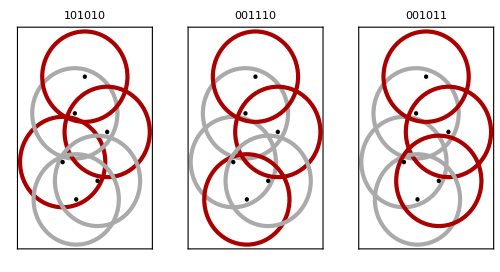

```mathematica
GraphicsRow[{plot[1],plot[2],plot[3]},ImageSize->500]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms\\Graphics"]
Export["101010c.jpg",plot[1]]
Export["001110c.jpg",plot[2]]
Export["001011c.jpg",plot[3]]
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms\Graphics

101010c.jpg

001110c.jpg

001011c.jpg

## Task 3 List Generation

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms"]
data=Import["task3_data.dat","List"];
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms

```mathematica
dataList=Table[StringTake[data[[i]],12],{i,1,Length[data]}];
```

```mathematica
Block[{t=SortBy[Tally[dataList],Last]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

Number | Frequency
000000011011 | 1
000001000011 | 1
000001000110 | 1
000001011011 | 1
000010010001 | 1
000010011011 | 1
000011000011 | 1
000011000100 | 1
000100010001 | 1
000100011000 | 1
000101011001 | 1
000111000110 | 1
001000011011 | 1
001001010011 | 1
001100011001 | 1
010000011000 | 1
010000101011 | 1
010000110011 | 1
010000111001 | 1
010001000100 | 1
010001011011 | 1
010010011001 | 1
010100011001 | 1
010101010001 | 1
011000000001 | 1
011000001011 | 1
011000001100 | 1
011000010001 | 1
011000100011 | 1
011000100110 | 1
011001000011 | 1
011001000110 | 1
011100011001 | 1
100000010001 | 1
100000100001 | 1
100000100010 | 1
100000101011 | 1
100001000010 | 1
100001000100 | 1
100001000111 | 1
100001011001 | 1
100011000011 | 1
100011000110 | 1
100011011001 | 1
100100010011 | 1
100100011001 | 1
100101000110 | 1
101000010000 | 1
101000011010 | 1
101001000110 | 1
101010010011 | 1
110000011001 | 1
110001000110 | 1
110001010000 | 1
110001010001 | 1
110001010010 | 1
111000000001 | 1
111000000010 | 1
111000010000 | 1
111000010001 | 1
111000010010 | 1
111000011000 | 1
000010010011 | 2
000100011011 | 2
000101000011 | 2
010000001001 | 2
010000011011 | 2
011000000010 | 2
011000010000 | 2
100000011011 | 2
100000111001 | 2
100001100110 | 2
111000001001 | 2
000000011001 | 3
000011010001 | 3
000100010011 | 3
000110011001 | 3
100010011001 | 3
111000000110 | 3
111000011011 | 3
010000100110 | 4
010101000110 | 4
100000010011 | 4
111001010011 | 4
000101010001 | 5
010001011001 | 5
101000000011 | 5
010000010011 | 6
100001010010 | 6
010001010001 | 7
101000011000 | 7
010000100011 | 8
100000100110 | 8
101000001001 | 8
010001010010 | 9
011000000011 | 9
100001010001 | 9
101000010001 | 10
011000011000 | 11
100000011001 | 14
100000100011 | 14
100001000011 | 17
101000000110 | 17
001000011001 | 19
010001000011 | 19
010001000110 | 19
011000000110 | 19
011000001001 | 20
010000011001 | 23
100001000110 | 23
010000101001 | 25
111000011001 | 25
010011010011 | 26
100000101001 | 26
000101000110 | 27
011000010010 | 27
100101010011 | 28
101000010010 | 30
000011000110 | 32
100011010011 | 33
000010011001 | 35
000111010011 | 36
001000010011 | 37
010101010011 | 38
101000011011 | 45
111000010011 | 49
000100011001 | 51
011000011011 | 53
110001010011 | 56
101001010011 | 90
011001010011 | 99
000001010011 | 125
011000011001 | 283
101000011001 | 292
000101010011 | 964
000011010011 | 974
011000010011 | 1255
101000010011 | 1276
100001010011 | 1753
010001010011 | 1772

## Task 2 Visualization (The bit-string order is Reversed!)

```mathematica
graph1={{1.19,4.25},{2.71,3.48},{1.19,3.51},{2,3.38},{1.12,2.86},{1.70,2.42},{2.36,2.54},{1.52,1.48},{2.15,1.54},{2.14,1.87},{1.72,0.86},{2.29,0.87}};
solLabels={"011000010011","101000010011","100001010011","010001010011"};
Do[f[j]={},{j,1,4}];
Do[If[StringPart[solLabels[[j]], i]=="1",f[j]=Append[f[j],13-i]],{i,1,12},{j,1,4}]
solutions=Table[f[j],{j,1,4}]
```

{{11,10,5,2,1},{12,10,5,2,1},{12,7,5,2,1},{11,7,5,2,1}}

```mathematica
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=0.5;
color1=Lighter[Gray];
color2=Darker[Red];
colorList={If[MemberQ[solutions[[i1]],1],color2,color1],If[MemberQ[solutions[[i1]],2],color2,color1],If[MemberQ[solutions[[i1]],3],color2,color1],If[MemberQ[solutions[[i1]],4],color2,color1],If[MemberQ[solutions[[i1]],5],color2,color1],If[MemberQ[solutions[[i1]],6],color2,color1],If[MemberQ[solutions[[i1]],7],color2,color1],If[MemberQ[solutions[[i1]],8],color2,color1],If[MemberQ[solutions[[i1]],9],color2,color1],If[MemberQ[solutions[[i1]],10],color2,color1],If[MemberQ[solutions[[i1]],11],color2,color1],If[MemberQ[solutions[[i1]],12],color2,color1]};bList={#}&/@graph1;
circles={colorList[[#]],AbsoluteThickness[3],Circle[graph1[[#]],T]}&/@Table[i,{i,1,12}];
dots={Black,Disk[graph1[[#]],0.05]}&/@Table[i,{i,1,12}];
Graphics[Flatten[{circles,dots},1],Frame->True,FrameTicks->None]]
```

-Graphics-

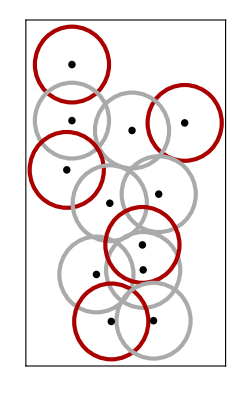

```mathematica
GeoListPlot[GeoPosition[#]&/@graph1]
```

{{1.19,-4.25},{2.71,-3.48},{1.19,-3.51},{2,-3.38},{1.12,-2.86},{1.7,-2.42},{2.36,-2.54},{1.52,-1.48},{2.15,-1.54},{2.14,-1.87},{1.72,-0.86},{2.29,-0.87}}

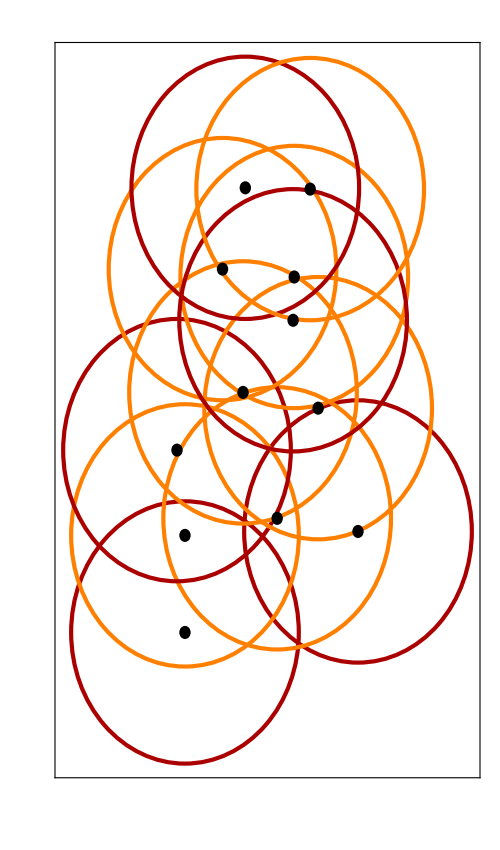
-Graphics--Graphics-

```mathematica
Img=-Graphics-;
Img=ImageAdjust[Img,{0,4}];
graph1={{1.19,-4.25},{2.71,-3.48},{1.19,-3.51},{2,-3.38},{1.12,-2.86},{1.70,-2.42},{2.36,-2.54},{1.52,-1.48},{2.15,-1.54},{2.14,-1.87},{1.72,-0.86},{2.29,-0.87}}
plot[i1_]:=Module[{T,colorList,bList,circles,color2,color1,dots},
T=1;
color1=Orange;
color2=Darker[Red];
colorList={If[MemberQ[solutions[[i1]],1],color2,color1],If[MemberQ[solutions[[i1]],2],color2,color1],If[MemberQ[solutions[[i1]],3],color2,color1],If[MemberQ[solutions[[i1]],4],color2,color1],If[MemberQ[solutions[[i1]],5],color2,color1],If[MemberQ[solutions[[i1]],6],color2,color1],If[MemberQ[solutions[[i1]],7],color2,color1],If[MemberQ[solutions[[i1]],8],color2,color1],If[MemberQ[solutions[[i1]],9],color2,color1],If[MemberQ[solutions[[i1]],10],color2,color1],If[MemberQ[solutions[[i1]],11],color2,color1],If[MemberQ[solutions[[i1]],12],color2,color1]};bList={#}&/@graph1;
circles={colorList[[#]],AbsoluteThickness[3],Circle[graph1[[#]],T]}&/@Table[i,{i,1,12}];
dots={Black,Disk[graph1[[#]],0.05]}&/@Table[i,{i,1,12}];
Graphics[
Flatten[{circles,dots},1],Frame->True,FrameTicks->None,ImageSize->500,AspectRatio->1.7]]
image=Overlay[{Img,plot[1]},Alignment->Center]
```

```mathematica
Export["overlay.jpg",image]
```

overlay.jpg

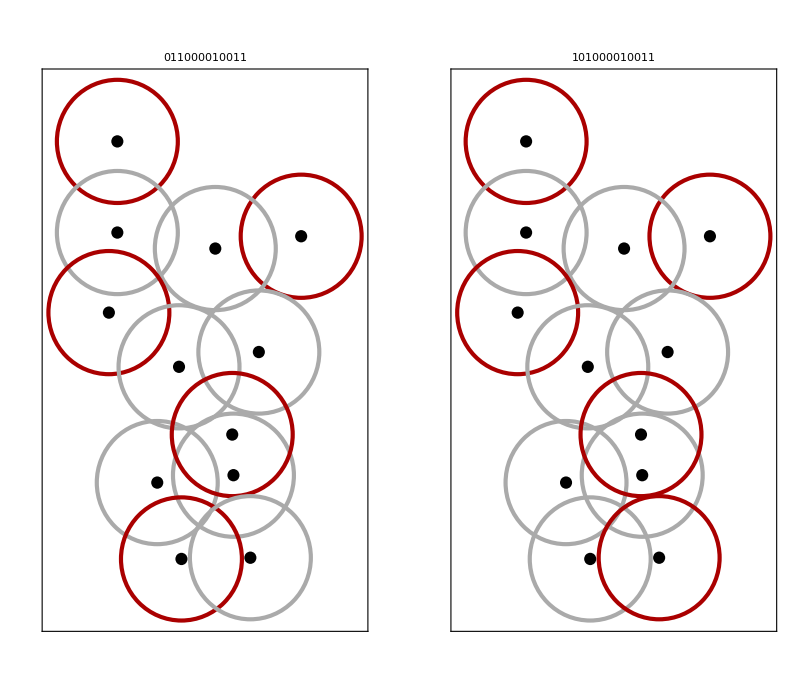

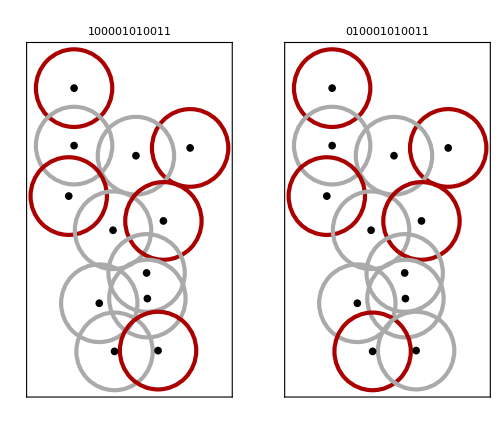

```mathematica
GraphicsRow[{plot[1],plot[2]},ImageSize->500]
GraphicsRow[{plot[3],plot[4]},ImageSize->500]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms\\Graphics"]
Export["011000010011c.jpg",plot[1]]
Export["101000010011c.jpg",plot[2]]
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms\Graphics

011000010011c.jpg

101000010011c.jpg

## Business Solution

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms"]
data=Import["task4_data.dat","List"];
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms

```mathematica
dataList=Table[StringTake[data[[i]],13],{i,1,Length[data]}];
```

```mathematica
Block[{t=SortBy[Tally[dataList],Last]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

Number | Frequency
0000111011011 | 1
0001001111011 | 1
0010001111101 | 1
0010100111011 | 1
0010111001011 | 1
0010111001101 | 1
0010111011001 | 1
0011011010101 | 1
0100011011101 | 1
0100100111101 | 1
0100101101101 | 1
0100101111100 | 1
0100111011001 | 1
0101001011011 | 1
0101001110011 | 1
0101001110101 | 1
0101001111001 | 1
0110111011011 | 1
1000001111011 | 1
1000011011101 | 1
1000101011011 | 1
1000101011101 | 1
1000111010011 | 1
1000111011001 | 1
1000111011010 | 1
1001000101101 | 1
1001000111011 | 1
1001001011101 | 1
1001001110101 | 1
1001001111010 | 1
1001011010011 | 1
1001011011100 | 1
1001011111011 | 1
1010000111101 | 1
1010001011011 | 1
1010001101011 | 1
1010010011101 | 1
1010011010011 | 1
1010011011010 | 1
1010011011100 | 1
1010100111001 | 1
1010101001011 | 1
1010101010011 | 1
1010101011001 | 1
1010101100101 | 1
1010101101100 | 1
1010110001011 | 1
1010110001101 | 1
1010110010001 | 1
1010110011011 | 1
1010111001001 | 1
1010111001111 | 1
1010111011000 | 1
1010111110101 | 1
1011000101101 | 1
1011000110011 | 1
1011001010011 | 1
1011001011001 | 1
1011001011010 | 1
1011001101010 | 1
1011010001101 | 1
1011010011010 | 1
1011011000011 | 1
1011011000101 | 1
1011011010001 | 1
1011101110101 | 1
1011111011101 | 1
1100001110011 | 1
1100001111000 | 1
1100010011011 | 1
1100011011111 | 1
1100011111011 | 1
1100100011101 | 1
1100100101001 | 1
1100101010011 | 1
1100101011001 | 1
1100101011010 | 1
1100101011100 | 1
1100101110001 | 1
1100101111000 | 1
1100101111010 | 1
1100110010101 | 1
1100110011001 | 1
1100111011000 | 1
1100111110101 | 1
1101000110011 | 1
1101000111010 | 1
1101000111100 | 1
1101001011100 | 1
1101001011111 | 1
1101001101001 | 1
1101001101010 | 1
1101001110111 | 1
1101010001011 | 1
1101011000011 | 1
1101011001001 | 1
1101011011000 | 1
1101011111001 | 1
1101110011011 | 1
1110011011101 | 1
1110111011010 | 1
1110111011011 | 1
1111001110011 | 1
1111011011001 | 1
0001011011101 | 2
0010011011011 | 2
0010101101011 | 2
0011001111001 | 2
0100101111001 | 2
1000011011011 | 2
1000101110101 | 2
1000101111001 | 2
1000110011011 | 2
1000111001101 | 2
1001001111001 | 2
1001111011101 | 2
1010001110011 | 2
1010001110101 | 2
1010100110101 | 2
1010111111101 | 2
1011001111000 | 2
1011011111101 | 2
1100001011101 | 2
1100010011101 | 2
1100011001101 | 2
1100011011001 | 2
1100011011100 | 2
1100100110101 | 2
1100111001010 | 2
1101001010101 | 2
1101001111000 | 2
1101011011111 | 2
1111001111010 | 2
0010101111001 | 3
1001001011011 | 3
1001001101101 | 3
1011001110001 | 3
1011011010011 | 3
1100001110101 | 3
1100111011100 | 3
1101000011101 | 3
1101011001101 | 3
1101111011101 | 3
1111001111011 | 3
1111011011011 | 3
0100111011011 | 4
1010011011001 | 4
1011101111011 | 4
1011111011011 | 4
1100001111001 | 4
1100101111100 | 4
1100101111111 | 4
1101011111101 | 4
0011011011011 | 5
0101001111101 | 5
1000001111101 | 5
1010101111111 | 5
1011011011010 | 5
1100111111101 | 5
1101111011011 | 5
1110101111011 | 5
1110111011101 | 5
1010111111011 | 6
1011001111010 | 6
1011001111111 | 6
1100101110101 | 6
1100111011111 | 6
1100111111011 | 6
1101011111011 | 6
1101101111011 | 6
1111001111101 | 6
1111011011101 | 6
1010100111101 | 7
1010101111010 | 7
1010111011111 | 7
1011011011111 | 7
1100111001011 | 7
1101010011011 | 7
1101101111101 | 7
0010101111101 | 8
0100101111011 | 8
0100101111101 | 8
1010101110011 | 8
1010101110101 | 8
1010101111100 | 8
1010111001101 | 8
1010111011010 | 8
1011001101011 | 8
1011001110011 | 8
1011011010101 | 8
1011101111101 | 8
1100101110011 | 8
1100110011011 | 8
1101001101101 | 8
1101011011100 | 8
1110101111101 | 8
0011001111011 | 9
1010101101011 | 9
1011000111011 | 9
1011010011101 | 9
1011011001011 | 9
1011011011100 | 9
1011011111011 | 9
1100101101101 | 9
1100111001101 | 9
1100111010101 | 9
1101000111101 | 9
1101001110011 | 9
1101001111100 | 9
1101011010101 | 9
0011001111101 | 10
0101011011011 | 10
0101011011101 | 10
1010101101101 | 10
1011001101101 | 10
1011001110101 | 10
1101000111011 | 10
0010101111011 | 11
0010111011101 | 11
0100111011101 | 11
1010100111011 | 11
1010110011101 | 11
1010111010011 | 11
1011011001101 | 11
1101001111111 | 11
1101010011101 | 11
1101011011010 | 11
0101001111011 | 12
1010111010101 | 12
1011000111101 | 12
1100101101011 | 12
0010111011011 | 13
0011011011101 | 13
1010111011100 | 13
1011001111100 | 13
1101001110101 | 13
1011010011011 | 14
1100100111101 | 14
1100110011101 | 14
1101001111010 | 14
1101011001011 | 14
1101011010011 | 14
1100111010011 | 15
1101001101011 | 15
1100111011010 | 16
1010111001011 | 18
1100100111011 | 18
1000101111011 | 19
1001001111011 | 20
1101001011101 | 20
1010101111001 | 21
1100011011101 | 21
1101001111001 | 21
1010001111011 | 22
1010111011001 | 22
1000111011101 | 25
1001001111101 | 25
1001011011011 | 25
1010101011101 | 25
1000101111101 | 26
1000111011011 | 27
1100101111001 | 27
1001011011101 | 28
1010011011011 | 29
1011001111001 | 29
1100001111101 | 29
1101011011001 | 29
1011001011101 | 30
1100011011011 | 30
1010011011101 | 32
1011001011011 | 32
1011011011001 | 32
1010001111101 | 33
1010101011011 | 33
1100001111011 | 33
1101001011011 | 34
1100111011001 | 35
1100101011011 | 37
1100101011101 | 38
1010111011011 | 448
1101011011011 | 465
1100111011011 | 467
1101001111101 | 489
1101001111011 | 490
1100111011101 | 492
1101011011101 | 499
1010101111101 | 505
1011011011011 | 507
1010101111011 | 509
1011001111011 | 511
1011001111101 | 514
1100101111101 | 514
1100101111011 | 524
1011011011101 | 532
1010111011101 | 540

```mathematica
Length[graph2]
```

13

```mathematica
graph2={{40.77912258043522,-73.98454494478796},{40.77574281493932,-73.99038143102224},{40.76898276810238,-73.98042507215202},{40.765862514512946,-73.99724788541549},{40.76274211441795,-73.98523159022729},{40.762482074463655,-73.9776784903947},{40.75832129683225,-73.9869482038256},{40.75780118131573,-73.99930782173348},{40.75494047323415,-73.99450130365818},{40.75364011068508,-73.97561855407673},{40.74687781544779,-73.97252864959975},{40.74557729521456,-74.00411433980875}};
```

```mathematica
solLabels={"1010111011101","1011011011101","1100101111011"};
Do[f[j]={},{j,1,4}];
Do[If[StringPart[solLabels[[j]], i]=="1",f[j]=Append[f[j],14-i]],{i,1,13},{j,1,3}]
solutions=Table[f[j],{j,1,3}]
```

{{13,11,9,8,7,5,4,3,1},{13,11,10,8,7,5,4,3,1},{13,12,9,7,6,5,4,2,1}}

```mathematica
solutions[[1]]
```

```mathematica
{13,11,10}
```

-Graphics-

```mathematica
rs=75;
s1=1.35*rs;
s2=0.8*1*rs;
s3=1.15*rs;
Show[GeoListPlot[GeoPosition[#]&/@graph2[[{2,3}]],PlotMarkers->{"◯",Scaled[s1]},PlotStyle->Black],
GeoListPlot[GeoPosition[#]&/@graph2[[{3}]],PlotMarkers->{"◯",Scaled[s1]},PlotStyle->Red],

GeoListPlot[GeoPosition[#]&/@graph2[[{4,5,6}]],PlotMarkers->{"◯",Scaled[s2]},PlotStyle->Black],
GeoListPlot[GeoPosition[#]&/@graph2[[{4,5}]],PlotMarkers->{"◯",Scaled[s2]},PlotStyle->Red],

GeoListPlot[GeoPosition[#]&/@graph2[[{10,11,12,13}]],PlotMarkers->{"◯",Scaled[s1]},PlotStyle->Black],
GeoListPlot[GeoPosition[#]&/@graph2[[{11,13}]],PlotMarkers->{"◯",Scaled[s1]},PlotStyle->Red],

GeoListPlot[GeoPosition[#]&/@graph2[[{7,8,9}]],PlotMarkers->{"◯",Scaled[s3]},PlotStyle->Red]
]
```

-Graphics-

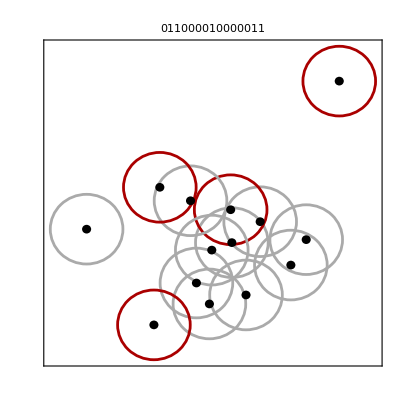

```mathematica
plot[1]
```